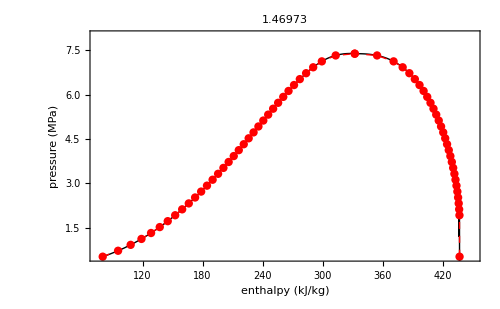
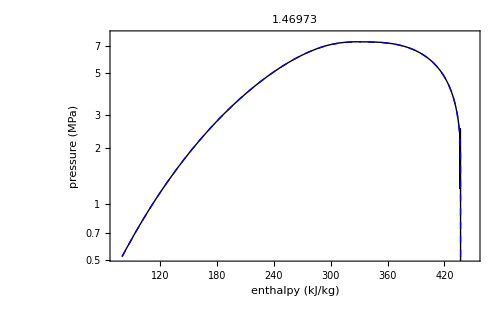
-Graphics- | -Graphics-

```mathematica
Module[{cond,HL,HV,hL,hV,enthalpy,p1,p2,p3,p4},

HL={(*{"HL (kJ/kg)","P (MPa)"},*){80.212,0.52},{95.578,0.72},{108.16,0.92},{118.97,1.12},{128.56,1.32},{137.25,1.52},{145.24,1.72},{152.68,1.92},{159.67,2.12},{166.29,2.32},{172.6,2.52},{178.65,2.72},{184.48,2.92},{190.11,3.12},{195.59,3.32},{200.92,3.52},{206.14,3.72},{211.25,3.92},{216.28,4.12},{221.25,4.32},{226.17,4.52},{231.05,4.72},{235.92,4.92},{240.79,5.12},{245.69,5.32},{250.63,5.52},{255.64,5.72},{260.76,5.92},{266.03,6.12},{271.52,6.32},{277.32,6.52},{283.61,6.72},{290.69,6.92},{299.33,7.12},{313.2,7.32},{332.25,7.38}};
(*HV={(*{"HV (kJ/kg)","P (MPa)"},*)(*{430.45,0.52},{433.09,0.72},{434.79,0.92},{435.9,1.12},{436.59,1.32},{436.95,1.52},*){437.06,0.52},(**){437,1},{436.97,1.5},(**){436.96,1.92},{436.65,2.12},{436.2,2.32},{435.6,2.52},{434.86,2.72},{433.99,2.92},{433.,3.12},{431.9,3.32},{430.67,3.52},{429.33,3.72},{427.87,3.92},(**){426.28,4.12},{424.56,4.32},{422.71,4.52},{420.72,4.72},{418.57,4.92},{416.24,5.12},{413.72,5.32},{410.99,5.52},{408.01,5.72},{404.73,5.92},{401.09,6.12},{397.01,6.32},{392.35,6.52},{386.87,6.72},{380.15,6.92},{371.08,7.12},{354.57,7.32},{332.25,7.38}};*)
HV={(*{"HV (kJ/kg)","P (MPa)"},*){437.06,0.52},{436.96,1.92},{436.65,2.12},{436.2,2.32},{435.6,2.52},{434.86,2.72},{433.99,2.92},{433.,3.12},{431.9,3.32},{430.67,3.52},{429.33,3.72},{427.87,3.92},{426.28,4.12},{424.56,4.32},{422.71,4.52},{420.72,4.72},{418.57,4.92},{416.24,5.12},{413.72,5.32},{410.99,5.52},{408.01,5.72},{404.73,5.92},{401.09,6.12},{397.01,6.32},{392.35,6.52},{386.87,6.72},{380.15,6.92},{371.08,7.12},{354.57,7.32},{332.25,7.38}};
hL=Interpolation[HL];hV=Interpolation[HV];
enthalpy=Piecewise[{{hL,80.212≤h≤332.25},{hV,332.25<h≤437.1}}];

cond=Sequence[Frame->True,FrameLabel->{Style["enthalpy (kJ/kg)",17],Style["pressure  (MPa)",17]},LabelStyle->{Black,14},Axes->False,ImageSize->{500,350},PlotLabel->hV[437]];

p1=Plot[enthalpy[h],{h,80.212,437.1},PlotStyle->{Thick,Black}];
p2=ListPlot[{HL,HV},Joined->True,PlotStyle->{{Thick,Dashed,Red}},Mesh->All];

p3=LogPlot[enthalpy[h],{h,80.212,437.1},PlotStyle->{Thick,Black}];
p4=ListLogPlot[{HL,HV},Joined->True,PlotStyle->{{Thick,Dashed,Blue}}(*,Mesh->All,MeshStyle->Directive[PointSize[0.01]]*)];

Grid[{{Framed@Show[p1,p2,PlotRange->{{75,450},{0.52,8}},Evaluate@cond],Framed@Show[p3,p4,PlotRange->{{75,450},{Log@0.52,Log@8}},Evaluate@cond]}}]
]
```

```mathematica
(*HV={(*{"HV (kJ/kg)","P (MPa)"},*){430.45,0.52},{433.09,0.72},{434.79,0.92},{435.9,1.12},{436.59,1.32},{436.95,1.52},{437.06,1.72},{436.96,1.92},{436.65,2.12},{436.2,2.32},{435.6,2.52},{434.86,2.72},{433.99,2.92},{433.,3.12},{431.9,3.32},{430.67,3.52},{429.33,3.72},{427.87,3.92},{426.28,4.12},{424.56,4.32},{422.71,4.52},{420.72,4.72},{418.57,4.92},{416.24,5.12},{413.72,5.32},{410.99,5.52},{408.01,5.72},{404.73,5.92},{401.09,6.12},{397.01,6.32},{392.35,6.52},{386.87,6.72},{380.15,6.92},{371.08,7.12},{354.57,7.32},{332.25,7.38}};*)
```

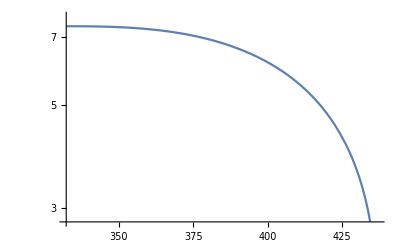

```mathematica
poo={(*{430.45,0.52},
{433.09,0.72},
{434.79,0.92},
{435.9,1.12},
{436.59,1.32},
{436.95,1.52},*)
{437.06,1.72},
{436.96,1.92},
{436.65,2.12},
{436.2,2.32},
{435.6,2.52},
{434.86,2.72},
{433.99,2.92},
{433.,3.12},
{431.9,3.32},
{430.67,3.52},
{429.33,3.72},
{427.87,3.92},(**)
{426.28,4.12},
{424.56,4.32},
{422.71,4.52},
{420.72,4.72},
{418.57,4.92},
{416.24,5.12},
{413.72,5.32},
{410.99,5.52},
{408.01,5.72},
{404.73,5.92},
{401.09,6.12},
{397.01,6.32},
{392.35,6.52},
{386.87,6.72},
{380.15,6.92},
{371.08,7.12},
{354.57,7.32},
{332.25,7.38}};
doo=Interpolation[poo];
LogPlot[doo[x],{x,332.25,437.06}]
```